# Tonks-Girardeau gas: the Bethe Ansatz solution in a random finite lattice, analytical form

```mathematica
Import["/Users/irina 1/qsu_repo/bethe_ansatz/RandomLattice.png"]
```

Import::nffil: File not found during Import.

$Failed

## One particle case

Here I define all the parameters of the system.

```mathematica
numBar=7; (* Total number of the delta barriers*)
barHeight = 5.5
ys = Symbol["y"<>ToString[#]]&/@Range[1,numBar] (*List of the variables (placeholders) for the positions of the barriers*)
ds=Symbol["d"<>ToString[#]]&/@Range[1,numBar](*List of the variables (placeholders) for the heights of the barriers*)
specificRules = {L->10, ℏ->1, m->1}; (*Rules to fix the length of the box L, and the ℏ/m ratio*)
$Assumptions=Element[ds, Reals]&&Element[ys, Reals]&&Element[L, Reals] &&Element[m, Reals]&& Element[ℏ, Reals]&&Element[k, Reals](*General assumptions about parameters. They are all real.*)
```

5.5

{y1,y2,y3,y4,y5,y6,y7}

{d1,d2,d3,d4,d5,d6,d7}

(d1|d2|d3|d4|d5|d6|d7)∈Reals&&(y1|y2|y3|y4|y5|y6|y7)∈Reals&&L∈Reals&&m∈Reals&&ℏ∈Reals&&k∈Reals

Here I define cyclic permutation of the barriers with Δ∈[-L, L] shift. Note that for negative Δ the effective shift is equivalent to  L+Δ shift. This is precisely what function Mod[Δ, L] is doing.

```mathematica
(* Cyclic permutation of the barrier heights *)
cyclicBarrierShiftHeights[Δ_, ys_, ds_, L_]:=Module[{shift, signs, dels, resultDs, Nb},(Nb = Length[ds];dels=Flatten[{L/2-#&/@ Reverse[ys], L}];signs=Sign[Mod[Δ,L] - dels]; shift=Floor[Total[signs + 1]/2];resultDs = Flatten[{ds[[Nb-shift+1;;Nb]],ds[[1;;Nb-shift]]}])]
(* Cyclic permutation of the barrier positions *)
cyclicBarrierShiftPos[Δ_, ys_, L_]:=Module[{Nb, resultYs},(Nb = Length[ds];resultYs = Sort[Mod[ys+Δ + L/2, L]-L/2])]
```

## The Bethe equations

Here we construct a Bethe Equation according to

-Graphics-

```mathematica
𝒯[n_, ys_, ds_]:= Module[{combs},(combs=Subsets[Range[1,Length[ys]], {n}];2^(2n)Total[Times@@(ds[[#]] m/ℏ^2)If[Length[#]>=1, Sin[k(ys[[#]][[1]]+L/2)]Sin[k(L/2-ys[[#]][[n]])], Sin[k L]]Product[Sin[k(ys[[#]][[j]]-ys[[#]][[j-1]])],{j,2,n}]&/@combs])]
𝒯[1, ys, ds];
```

```mathematica
makeBE[ys_, ds_]:=Sum[𝒯[n, ys, ds] k^(Length[ds]-n), {n, 0, Length[ds]}]==0
AbsoluteTiming[TGBE=makeBE[ys, ds];]
```

{0.012303,Null}

## The Coefficients

Here I reconstruct the coefficients and the normaliation constant accroding to

-Graphics-

```mathematica
(*n is the number of the well in which the particle is in, for 1-particle case. The coefficient we are calculating is Subscript["𝒜", {1,0,0,0,0}][{k1}], with 1 in the well number n.  ds - heights of the barriers, ys - positions of the barriers*)
makeCoef[n_, ds_, ys_]:=Module[{combs, posCombs, elems, curProd, curYP},(combs=Subsets[Range[1,n-1], n-1]; elems = Total[(Times@@(ds[[#]]*(-2 m ⅈ)/(k ℏ^2))If[Length[#]>0,(1-Exp[-ⅈ k (L + 2 ys[[#]][[1]])]), 1])Product[(1-Exp[-ⅈ 2 k (+ys[[#]][[j]]-ys[[#]][[j-1]])]), {j, 2, Length[#]}]&/@combs])];
makeCoef[2, ds, ys];
```

```mathematica
(*Real part of a coefficient*)
```

```mathematica
realPartMakeCoef[n_, ds_, ys_]:=Module[{combs, posCombs, elems, curProd, curYP},(combs=Subsets[Range[1,n-1], n-1]; elems = Total[(Times@@(ds[[#]])((-4 m)/(k ℏ^2))^Length[#] If[Length[#]>0,(-Sin[k(L/2+ys[[#]][[1]])]Cos[k(ys[[#]][[Length[#]]]+L/2)]), 1])Product[(Sin[ k (-ys[[#]][[j]]+ys[[#]][[j-1]])]), {j, 2, Length[#]}]&/@combs])];
realPartMakeCoef[2, ds, ys];
```

```mathematica
(*Imaginary part of a coefficient *)
```

```mathematica
imPartMakeCoef[n_, ds_, ys_]:=Module[{combs, posCombs, elems, curProd, curYP},(combs=Subsets[Range[1,n-1], {1,n-1}]; elems = Total[(Times@@(ds[[#]])((-4 m)/(k ℏ^2))^Length[#] If[Length[#]>0,(Sin[k(L/2+ys[[#]][[1]])]Sin[k(ys[[#]][[Length[#]]]+L/2)]), 1])Product[(Sin[ k (-ys[[#]][[j]]+ys[[#]][[j-1]])]), {j, 2, Length[#]}]&/@combs])];
imPartMakeCoef[2, {d1,d2,d3}, {y1,y2,y3}];
```

```mathematica
(* Calculate the normalization constant*)
```

```mathematica
calcNorm[ds_, ys_]:= Module[{ReA, ImA, ReA1, ImA1},(ReA1 = realPartMakeCoef[numBar+1, ds, ys]; ImA1=imPartMakeCoef[numBar+1, ds, ys];2 (ys[[1]]+L/2 + (-(Sin[k(L+2ys[[1]])]))/(2 k)) + 2 Total[(ReA =realPartMakeCoef[#, ds, ys];ImA=imPartMakeCoef[#, ds, ys]; ReA^2(ys[[#]]-ys[[#-1]] + (-(Sin[k(L+2ys[[#]])]-Sin[k (L+2ys[[#-1]])]))/(2 k)) + ImA^2(ys[[#]]-ys[[#-1]] - (-(Sin[k(L+2ys[[#]])]-Sin[k (L+2ys[[#-1]])]))/(2 k)) - ReA ImA(Cos[k(L+2ys[[#]])]-Cos[k (L+2ys[[#-1]])])/k)&/@Range[2, numBar]]+2(ReA1^2(L/2-ys[[numBar]] + (-(Sin[k 2 L]-Sin[k (L+2ys[[numBar]])]))/(2 k)) + ImA1^2(L/2-ys[[numBar]] - (-(Sin[k 2 L]-Sin[k (L+2ys[[numBar]])]))/(2 k)) - ReA1 ImA1(Cos[k 2 L]-Cos[k (L+2ys[[numBar]])])/k))]
```

## Actual solution

```mathematica
a = γ * L/(numBar-1);
y0  = -L/2+(L-(numBar-1)a)/2;
randYsAllDelta=(y0+a*(#) + δ (y0+L/2))/.specificRules&/@Range[0, numBar-1]//FullSimplify;
(*randYsAllDelta=((-L/2 + L/(2(numBar)))+L/numBar(#) + δ L/(2(numBar))(**Mod[#,2]*))/.specificRules&/@Range[0, numBar-1];*)
thumorse={0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0};
randDs =(barHeight+0*Mod[#+0,2])&/@Range[1, numBar](* RandomReal[{0, 3}, Length[ds]]*)(*(1)&/@Range[1, numBar]*) ;
(*randDs[[{-7, -6}]] = 0;*)
randDs =(dh+0*Mod[#+0,2])&/@Range[1, numBar]
randRulesAllDelta= Flatten[{ys[[#]]->randYsAllDelta[[#]],ds[[#]]->randDs[[#]]}&/@Range[1, Length[ds]]]
allYsAllDelta=ys[[#]]->randYsAllDelta[[#]]&/@Range[1, Length[ds]];
```

{dh,dh,dh,dh,dh,dh,dh}

{y1→-5 (γ+(-1+γ) δ),d1→dh,y2→5 δ-5/3 γ (2+3 δ),d2→dh,y3→-5/3 (γ+3 (-1+γ) δ),d3→dh,y4→-5 (-1+γ) δ,d4→dh,y5→γ (5/3-5 δ)+5 δ,d5→dh,y6→γ (10/3-5 δ)+5 δ,d6→dh,y7→5 (γ+δ-γ δ),d7→dh}

```mathematica
a = γ * L/(numBar-1);
y0  = (L(-γ ))/2;
y0 + a*x =   (γ L(2  -(nb-1)*x))/(2*(numBar-1))
```

Set::write: Tag Plus in -(L γ)/2+(L x γ)/6 is Protected.

1/12 L (2-(-1+nb) x) γ

```mathematica
(y0+a*(#))&/@Range[0, numBar-1]//FullSimplify
```

{-(L γ)/2,-(L γ)/3,-(L γ)/6,0,(L γ)/6,(L γ)/3,(L γ)/2}

```mathematica
-L/2
```

-L/2

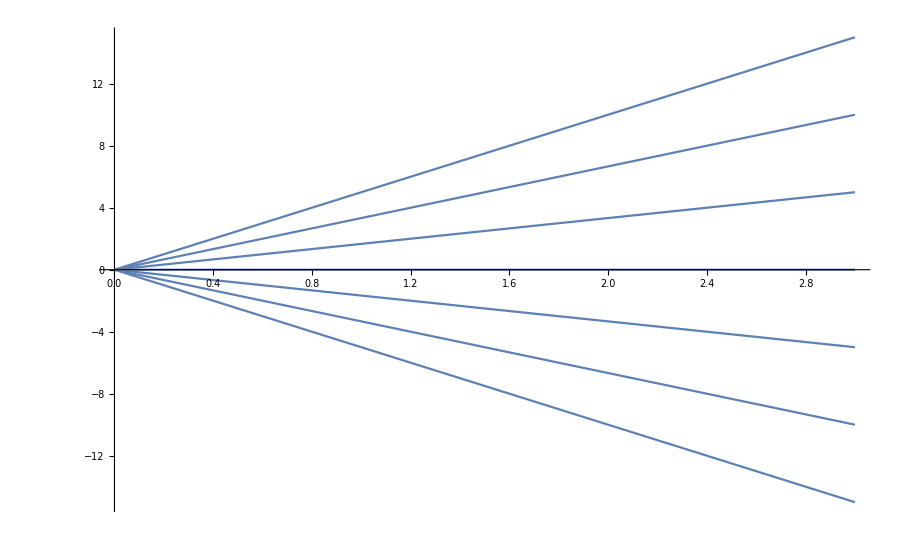

```mathematica
Plot[randYsAllDelta/.Flatten[{specificRules, δ->0}], {γ, 0, 3}]
```

```mathematica
(*cyclicBarrierShiftHeights[ -2, randYsAllDelta, ds, L/.specificRules];
Plot[cyclicBarrierShiftPos[Δ, randYsAllDelta, L/.specificRules][[1]], {Δ, -5,5}];*)
```

```mathematica
randYsAllDelta/.{δ->0}
```

{-5 γ,-(10 γ)/3,-(5 γ)/3,0,(5 γ)/3,(10 γ)/3,5 γ}

```mathematica
Solve[randYsAllDelta[[2]]== 10/6, γ]
```

{{γ→(-1+3 δ)/(2+3 δ)}}

```mathematica
bEF = Experimental`CreateNumericalFunction[{k,g},{TGBE[[1]]/.Flatten[{randRulesAllDelta, specificRules}]/.{δ->0, γ->g}}, {1}, Compiled->True];
```

```mathematica
bEF[{1,0.5}]
bEF["CompiledFunction"][1,0.5]
```

Experimental`NumericalFunction::nlnum: The function value {-0.544021+10.5721 dh+28.6095 dh^2-218.63 dh^3-380.237 dh^4+870.19 dh^5+1984.03 dh^6+964.986 dh^7} is not a list of numbers with dimensions {1} at {k,g} = {1.,0.5}.

Experimental`NumericalFunction[{k,g},{k^7 Sin[10 k]+16384 dh^7 Sin[(5-5 g) k]^2 Sin[(5 g k)/3]^6+4096 k (2 dh^6 Sin[(5-5 g) k] Sin[(5-(10 g)/3) k] Sin[(5 g k)/3]^5+5 dh^6 Sin[(5-5 g) k]^2 Sin[(5 g k)/3]^4 Sin[(10 g k)/3])+1024 k^2 (dh^5 Sin[(5-(10 g)/3) k]^2 Sin[(5 g k)/3]^4+2 dh^5 Sin[(5-5 g) k] Sin[(5-(5 g)/3) k] Sin[(5 g k)/3]^4+8 dh^5 Sin[(5-5 g) k] Sin[(5-(10 g)/3) k] Sin[(5 g k)/3]^3 Sin[(10 g k)/3]+6 dh^5 Sin[(5-5 g) k]^2 Sin[(5 g k)/3]^2 Sin[(10 g k)/3]^2+4 dh^5 Sin[(5-5 g) k]^2 Sin[(5 g k)/3]^3 Sin[5 g k])+256 k^3 (2 dh^4 Sin[5 k] Sin[(5-5 g) k] Sin[(5 g k)/3]^3+2 dh^4 Sin[(5-(10 g)/3) k] Sin[(5-(5 g)/3) k] Sin[(5 g k)/3]^3+3 dh^4 Sin[(5-(10 g)/3) k]^2 Sin[(5 g k)/3]^2 Sin[(10 g k)/3]+6 dh^4 Sin[(5-5 g) k] Sin[(5-(5 g)/3) k] Sin[(5 g k)/3]^2 Sin[(10 g k)/3]+6 dh^4 Sin[(5-5 g) k] Sin[(5-(10 g)/3) k] Sin[(5 g k)/3] Sin[(10 g k)/3]^2+dh^4 Sin[(5-5 g) k]^2 Sin[(10 g k)/3]^3+6 dh^4 Sin[(5-5 g) k] Sin[(5-(10 g)/3) k] Sin[(5 g k)/3]^2 Sin[5 g k]+6 dh^4 Sin[(5-5 g) k]^2 Sin[(5 g k)/3] Sin[(10 g k)/3] Sin[5 g k]+3 dh^4 Sin[(5-5 g) k]^2 Sin[(5 g k)/3]^2 Sin[(20 g k)/3])+64 k^4 (2 dh^3 Sin[5 k] Sin[(5-(10 g)/3) k] Sin[(5 g k)/3]^2+dh^3 Sin[(5-(5 g)/3) k]^2 Sin[(5 g k)/3]^2+4 dh^3 Sin[5 k] Sin[(5-5 g) k] Sin[(5 g k)/3] Sin[(10 g k)/3]+4 dh^3 Sin[(5-(10 g)/3) k] Sin[(5-(5 g)/3) k] Sin[(5 g k)/3] Sin[(10 g k)/3]+dh^3 Sin[(5-(10 g)/3) k]^2 Sin[(10 g k)/3]^2+2 dh^3 Sin[(5-5 g) k] Sin[(5-(5 g)/3) k] Sin[(10 g k)/3]^2+2 dh^3 Sin[(5-(10 g)/3) k]^2 Sin[(5 g k)/3] Sin[5 g k]+4 dh^3 Sin[(5-5 g) k] Sin[(5-(5 g)/3) k] Sin[(5 g k)/3] Sin[5 g k]+4 dh^3 Sin[(5-5 g) k] Sin[(5-(10 g)/3) k] Sin[(10 g k)/3] Sin[5 g k]+dh^3 Sin[(5-5 g) k]^2 Sin[5 g k]^2+4 dh^3 Sin[(5-5 g) k] Sin[(5-(10 g)/3) k] Sin[(5 g k)/3] Sin[(20 g k)/3]+2 dh^3 Sin[(5-5 g) k]^2 Sin[(10 g k)/3] Sin[(20 g k)/3]+2 dh^3 Sin[(5-5 g) k]^2 Sin[(5 g k)/3] Sin[(25 g k)/3]+2 dh^3 Sin[(5-5 g) k] Sin[(5 g k)/3]^2 Sin[(5+(5 g)/3) k])+16 k^5 (2 dh^2 Sin[5 k] Sin[(5-(5 g)/3) k] Sin[(5 g k)/3]+2 dh^2 Sin[5 k] Sin[(5-(10 g)/3) k] Sin[(10 g k)/3]+dh^2 Sin[(5-(5 g)/3) k]^2 Sin[(10 g k)/3]+2 dh^2 Sin[5 k] Sin[(5-5 g) k] Sin[5 g k]+2 dh^2 Sin[(5-(10 g)/3) k] Sin[(5-(5 g)/3) k] Sin[5 g k]+dh^2 Sin[(5-(10 g)/3) k]^2 Sin[(20 g k)/3]+2 dh^2 Sin[(5-5 g) k] Sin[(5-(5 g)/3) k] Sin[(20 g k)/3]+2 dh^2 Sin[(5-5 g) k] Sin[(5-(10 g)/3) k] Sin[(25 g k)/3]+dh^2 Sin[(5-5 g) k]^2 Sin[10 g k]+2 dh^2 Sin[(5-(10 g)/3) k] Sin[(5 g k)/3] Sin[(5+(5 g)/3) k]+2 dh^2 Sin[(5-5 g) k] Sin[(10 g k)/3] Sin[(5+(5 g)/3) k]+2 dh^2 Sin[(5-5 g) k] Sin[(5 g k)/3] Sin[(5+(10 g)/3) k])+4 k^6 (dh Sin[5 k]^2+2 dh Sin[(5-(5 g)/3) k] Sin[(5+(5 g)/3) k]+2 dh Sin[(5-(10 g)/3) k] Sin[(5+(10 g)/3) k]+2 dh Sin[(5-5 g) k] Sin[(5+5 g) k])},-NumericalFunctionData-][{1,0.5}]

$Failed

```mathematica
betheEquationsF[k_,g_]=TGBE[[1]]/.Flatten[{randRulesAllDelta, specificRules}]/.{δ->0, γ->g};
bECompiled = Compile[{k, g}, betheEquationsF[k,g]]
rationalGammas = Range[0,3, 1/100];
momenta = Range[1,10,0.01];
(*butterflyValues = Flatten[Module[{g, kk},(g = rationalGammas[[#]];(kk=momenta[[#]];{g,kk,If[Abs[bEF["CompiledFunction"][kk, g][[1]]]<1^(-2), 1, 0]})&/@Range[1, Length[momenta]])&/@Range[1, Length[rationalGammas]]],1];
ListDensityPlot[butterflyValues, PlotLegends->Automatic, InterpolationOrder->0]*)
```

CompiledFunction[…]

```mathematica
betheEquations=TGBE[[1]]/.Flatten[{randRulesAllDelta, specificRules}]/.{δ->Δ,γ->(numBar-1)/numBar};
SetOptions[ContourPlot,BaseStyle->{FontFamily->"Times",FontSize->14}];
plotObj1=ContourPlot[{betheEquations==0},{Δ, -1,1}, {k, 1, 10}, PlotRange->Full, PlotLegends->Automatic, PlotPoints->100, FrameLabel->{"Δ", "k"}, AspectRatio->2 , Epilog->{Thin,{Green,Point[{-0.7,8.68}],Green,Point[{-0.7,4.38}], Black, Point[{-0.4,8.72}], Black,Point[{-0.4,4.95}]}}]
(*orderedPairs=First[Cases[plotObj,x_GraphicsComplex :>  First@x,Infinity]];
orderedSqrP={#[[1]], #[[2]]^2} &/@ orderedPairs;
lineData=Cases[plotObj,x_Line :>  x,Infinity];
linesIndex = Cases[lineData,Line[x_] :>  x,Infinity];
allLines = orderedSqrP[[#]]&/@ linesIndex;
Length[orderedPairs]
Length[lineData]*)
```

$Aborted

```mathematica
Delta=0;
GGamma = 1/3(*(numBar-1)/numBar*);
GGamma =(numBar-1)/(numBar+1);
(*GGamma= 0;*)
randYs=randYsAllDelta/.Flatten[{specificRules}](*Sort[RandomReal[{-L/2, L/2}/.specificRules, Length[ys]]]*)(*{3}*);
randRules =randRulesAllDelta/.Flatten[{specificRules}]
```

{y1→-5 (γ+(-1+γ) δ),d1→dh,y2→5 δ-5/3 γ (2+3 δ),d2→dh,y3→-5/3 (γ+3 (-1+γ) δ),d3→dh,y4→-5 (-1+γ) δ,d4→dh,y5→γ (5/3-5 δ)+5 δ,d5→dh,y6→γ (10/3-5 δ)+5 δ,d6→dh,y7→5 (γ+δ-γ δ),d7→dh}

```mathematica
(*plotObj=ContourPlot[Evaluate[{TGBE/.k->k1, TGBE/.k->k2}//.Flatten[{specificRules, δ->Delta, γ->GGamma, randRules}]], {k1, -0.1, 9}, {k2, -0.1, 5}, PlotPoints->300,PlotLegends->Automatic, FrameLabel->{"k1", "k2"}]*)
```

```mathematica
(*sampleroots=Cases[(*Normal@*)plotObj,(*Line[pts_,___]:>pts*)GraphicsComplex[pts__]:>pts,Infinity];
ListPlot[#[[1]]&/@sampleroots[[1]]]*)
```

```mathematica
initPt ={3.9};
rootPt = FindRoot[TGBE//.Flatten[{specificRules, δ->Delta,γ->GGamma, randRules}],{k, #}]&/@initPt
```

FindRoot::nlnum: The function value {13226.3-16124.7 dh-107532. dh^2+57483.9 dh^3+121150. dh^4-54628.6 dh^5-32992.5 dh^6+14732.7 dh^7} is not a list of numbers with dimensions {1} at {k} = {3.9}.

{FindRoot[TGBE//.Flatten[{specificRules,δ→Delta,γ→GGamma,randRules}],{k,3.9}]}

```mathematica
(*K VALUES FOR WF!!!, solve for low barrier height*)
```

```mathematica
rootPt=NSolve[(TGBE//.Flatten[{specificRules, δ->Delta,γ->GGamma, randRules/.dh-> 5}])&&k > 0 && k <4,k, Reals, WorkingPrecision->20]
```

{{k→2.182702833136826662},{k→2.2159504125162037479},{k→2.2671462891769459462},{k→2.3301315134074941973},{k→2.3965436063073537202},{k→2.4561742067827214271},{k→2.4980966739674486356},{k→2.5132741228718345908}}

```mathematica
(TGBE[[1]]//.Flatten[{specificRules, δ->Delta,γ->GGamma, randRules, rootPt[[#]]}])&/@Range[1,Length[rootPt]]
```

{4.65661×10^-10,-4.65661×10^-10,2.32831×10^-10,7.27596×10^-12,2.27374×10^-12,-4.54747×10^-13,1.42109×10^-14,0.}

## The wave function

```mathematica
Acoeff[block_, P_]=Subscript["𝒜", block][P];
allBlocks[N_, barN_] := DeleteDuplicates[Flatten[Permutations[#]&/@(PadRight[#, barN+1]&/@IntegerPartitions[N, barN+1]),1]]
χ[wellN_, ds_, ys_] := Module[{ Ep}, (Ep ={k,-k}; ∑_(ne=1)^(Dimensions[Ep][[1]]) (-Exp[-ⅈ k L])^If[Refine[Sign[Ep[[ne]]],k>0]==1,0,1](makeCoef[ wellN,ds, ys]/.k->Ep[[ne]])Exp[ⅈ Ep[[ne]] x])]
Ψ[ds_,ys_, barN_] := Module[{bN, allB, N, dels, curWell, barHs, barPos,LL}, (N=1;allB=allBlocks[N, barN];
barPos=ys;
(*barPos = Flatten[{y0,ys,Symbol["y"<>ToString[barN+1]]}];LL=2 π/k Ceiling[L k/(2 π)];Total[(curWell=#;χ[curWell, ds, ys](Product[HeavisideTheta[-barPos[[i+1]]+Sign[x]Mod[Abs[x], LL]], {i, 0, curWell-1}]Product[HeavisideTheta[barPos[[i+1]]-Sign[x]Mod[Abs[x], LL]], {i, curWell,barN+1}]))&/@Range[1,barN+1]]*)
HeavisideTheta[x+L/2]HeavisideTheta[-x+L/2]Total[(curWell=#;χ[curWell, ds, ys]Product[HeavisideTheta[-barPos[[i]]+x], {i, 1, curWell-1}]Product[HeavisideTheta[barPos[[i]]-x], {i, curWell,barN}])&/@Range[1,barN+1]])]
```

```mathematica
(*WF is set, only depends on position now!*)
onePartWF[x_] =Ψ[ds,ys, numBar]//.Flatten[{specificRules, δ->Delta,γ->GGamma, randRules, #}]&/@rootPt;
```

```mathematica
(*change randRules, change k values i.e. rooPt*)
```

```mathematica
rootList = (k/.#)&/@rootPt
```

{2.2084653500735964309,2.2393805374830290702,2.2869104521353902103,2.3452281233744837344,2.406473993451834781,2.4611899483771569672,2.4994634091477639067,2.5132741228718345908}

```mathematica
ntoplot=Range[1,Length[rootPt]](*{numBar,2*numBar}*);

Flatten[{specificRules, δ->Delta, γ->GGamma,randRules, rootPt}]
nrmSymb = calcNorm[ds, ys];
normSqr = (nrmSymb//.Flatten[{δ->Delta,γ->GGamma,{randRules},{specificRules}, {#}}])&/@rootPt;
normSqr[[ntoplot]]
(*NIntegrate[Abs[onePartWF[x][[#]]]^2/1, Evaluate[ ({x, -L/2, L/2}/.specificRules)]]&/@ntoplot*)
```

{L→10,ℏ→1,m→1,δ→0,γ→3/4,y1→-5 (γ+(-1+γ) δ),d1→5.5,y2→5 δ-5/3 γ (2+3 δ),d2→5.5,y3→-5/3 (γ+3 (-1+γ) δ),d3→5.5,y4→-5 (-1+γ) δ,d4→5.5,y5→γ (5/3-5 δ)+5 δ,d5→5.5,y6→γ (10/3-5 δ)+5 δ,d6→5.5,y7→5 (γ+δ-γ δ),d7→5.5,k→2.2084653500735964309,k→2.2393805374830290702,k→2.2869104521353902103,k→2.3452281233744837344,k→2.406473993451834781,k→2.4611899483771569672,k→2.4994634091477639067,k→2.5132741228718345908}

{287.766,74.5538,35.115,21.3913,15.1752,12.0216,10.4718,20.}

```mathematica
TGDensity=(Total@(Abs[onePartWF[x][[#]]]^2/normSqr[[#]]&/@ntoplot)[[1;;#]])&/@ntoplot;
```

```mathematica
SinglePartDensity = Abs[onePartWF[x][[#]]]^2/normSqr[[#]]&/@ntoplot;
```

```mathematica
SinglePartWFAbs = Abs[onePartWF[x][[#]]]/normSqr[[#]]&/@ntoplot;
```

```mathematica
SinglePartWFRe = Re[onePartWF[x][[#]]]/normSqr[[#]]&/@ntoplot;
```

```mathematica
SinglePartWFIm = Im[onePartWF[x][[#]]]/normSqr[[#]]&/@ntoplot;
```

{{-15/4,{}},{-5/2,{}},{-5/4,{}},{0,{}},{5/4,{}},{5/2,{}},{15/4,{}},{-5,Directive[GrayLevel[0],Thickness[Large]]},{5,Directive[GrayLevel[0],Thickness[Large]]}}

{k -> 2.2084653500735964309,k -> 2.2393805374830290702,k -> 2.2869104521353902103,k -> 2.3452281233744837344,k -> 2.4064739934518347810,k -> 2.4611899483771569672,k -> 2.4994634091477639067,k -> 2.5132741228718345908}

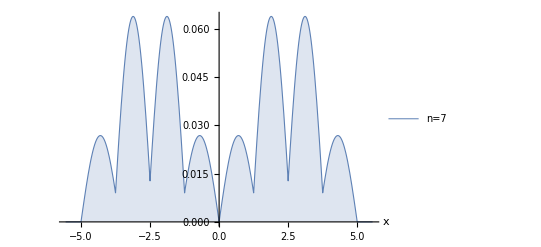

Documents/OIST/sze_out/mathematica/DPWFplot_TG_nbar_7_gamma_0.75_height_5.5_psi2_abs.png

Documents/OIST/sze_out/mathematica/DPWFplot_TG_nbar_7_gamma_0.75_height_5.5_psi2_abs.png

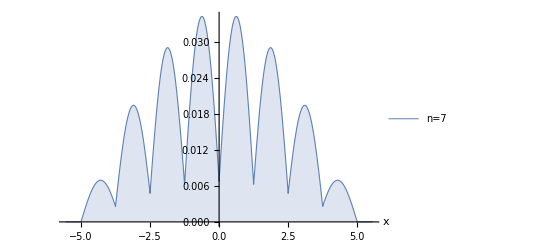

Documents/OIST/sze_out/mathematica/DPWFplot_TG_nbar_7_gamma_0.75_height_5.5_psi1_abs.png

Documents/OIST/sze_out/mathematica/DPWFplot_TG_nbar_7_gamma_0.75_height_5.5_psi1_abs.png

```mathematica
gridlns = Flatten[{randYs[[1;;-1]]/.{δ->Delta, γ->GGamma}, (-L/.specificRules)/2,(L/.specificRules)/2}];
glStyled=Flatten[{{gridlns[[#]], If[Mod[#,2]==1,{(*Dashed*)}, {(*Directive[Thick]*)}]}&/@ Range[1,Length[gridlns]-2],{{gridlns[[-2]], Directive[Black, Thick]}, {gridlns[[-1]], Directive[Black, Thick]}}},1]
legnd=Evaluate[ToString[#[[1]]]&/@rootPt]
SetOptions[Plot,BaseStyle->{FontFamily->"Times",FontSize->16, FontColor->Black}];
SPDP2 = Plot[Evaluate[SinglePartWFAbs[[2]](*[[{6,7}]]*)],Evaluate[ ({x, -L/1.8, L/1.8}/.specificRules)],GridLines -> {glStyled, {}}, PlotRange->Full(*, PlotStyle->{Blue}*), Evaluated->True, PlotLegends->{"n=7", "n=14"}(*legnd[[ntoplot]]*), PlotPoints->150, AxesLabel->{x, ""}, PlotStyle->{Thickness[0.005], Thickness[0.002]}, Filling->Bottom, Ticks->Automatic, Exclusions->None]

plotname = StringJoin["Documents/OIST/sze_out/mathematica/DPWFplot_TG_nbar_", ToString[numBar],"_gamma_", ToString[N[GGamma, 2]], "_height_",ToString[barHeight], "_psi2_abs",".png"]
Export[plotname, SPDP2]

SPDP1 = Plot[Evaluate[SinglePartWFAbs[[1]](*[[{6,7}]]*)],Evaluate[ ({x, -L/1.8, L/1.8}/.specificRules)],GridLines -> {glStyled, {}}, PlotRange->Full(*, PlotStyle->{Blue}*), Evaluated->True, PlotLegends->{"n=7", "n=14"}(*legnd[[ntoplot]]*), PlotPoints->150, AxesLabel->{x, ""}, PlotStyle->{Thickness[0.005], Thickness[0.002]}, Filling->Bottom, Ticks->Automatic, Exclusions->None]

plotname1 = StringJoin["Documents/OIST/sze_out/mathematica/DPWFplot_TG_nbar_", ToString[numBar],"_gamma_", ToString[N[GGamma, 2]], "_height_",ToString[barHeight], "_psi1_abs",".png"]
Export[plotname1, SPDP1]
```

```mathematica
4
```

4

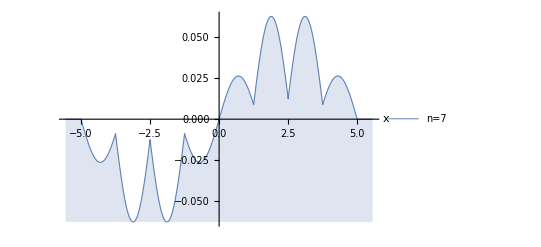

Documents/OIST/sze_out/mathematica/DPWFplot_TG_nbar_7_gamma_0.75_height_5.5_psi2_re.png

Documents/OIST/sze_out/mathematica/DPWFplot_TG_nbar_7_gamma_0.75_height_5.5_psi2_re.png

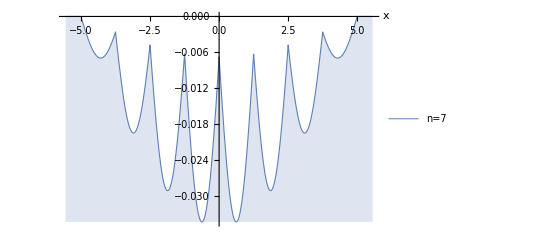

Documents/OIST/sze_out/mathematica/DPWFplot_TG_nbar_7_gamma_0.75_height_5.5_psi1_re.png

Documents/OIST/sze_out/mathematica/DPWFplot_TG_nbar_7_gamma_0.75_height_5.5_psi1_re.png

```mathematica
SPDP2re = Plot[Evaluate[SinglePartWFRe[[2]](*[[{6,7}]]*)],Evaluate[ ({x, -L/1.8, L/1.8}/.specificRules)],GridLines -> {glStyled, {}}, PlotRange->Full(*, PlotStyle->{Blue}*), Evaluated->True, PlotLegends->{"n=7", "n=14"}(*legnd[[ntoplot]]*), PlotPoints->150, AxesLabel->{x, ""}, PlotStyle->{Thickness[0.005], Thickness[0.002]}, Filling->Bottom, Ticks->Automatic, Exclusions->None]

plotname = StringJoin["Documents/OIST/sze_out/mathematica/DPWFplot_TG_nbar_", ToString[numBar],"_gamma_", ToString[N[GGamma, 2]], "_height_",ToString[barHeight], "_psi2_re",".png"]
Export[plotname, SPDP2re]

SPDP1re= Plot[Evaluate[SinglePartWFRe[[1]](*[[{6,7}]]*)],Evaluate[ ({x, -L/1.8, L/1.8}/.specificRules)],GridLines -> {glStyled, {}}, PlotRange->Full(*, PlotStyle->{Blue}*), Evaluated->True, PlotLegends->{"n=7", "n=14"}(*legnd[[ntoplot]]*), PlotPoints->150, AxesLabel->{x, ""}, PlotStyle->{Thickness[0.005], Thickness[0.002]}, Filling->Bottom, Ticks->Automatic, Exclusions->None]

plotname1 = StringJoin["Documents/OIST/sze_out/mathematica/DPWFplot_TG_nbar_", ToString[numBar],"_gamma_", ToString[N[GGamma, 2]], "_height_",ToString[barHeight], "_psi1_re",".png"]
Export[plotname1, SPDP1re]
```

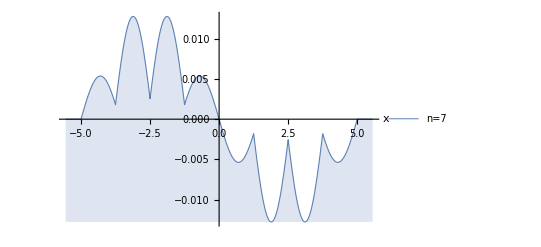

Documents/OIST/sze_out/mathematica/DPWFplot_TG_nbar_7_gamma_0.75_height_5.5_psi2_im.png

Documents/OIST/sze_out/mathematica/DPWFplot_TG_nbar_7_gamma_0.75_height_5.5_psi2_im.png

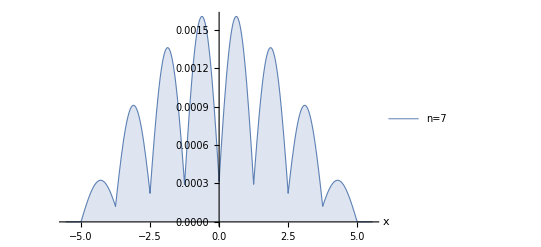

Documents/OIST/sze_out/mathematica/DPWFplot_TG_nbar_7_gamma_0.75_height_5.5_psi1_im.png

Documents/OIST/sze_out/mathematica/DPWFplot_TG_nbar_7_gamma_0.75_height_5.5_psi1_im.png

```mathematica
SPDP2im = Plot[Evaluate[SinglePartWFIm[[2]](*[[{6,7}]]*)],Evaluate[ ({x, -L/1.8, L/1.8}/.specificRules)],GridLines -> {glStyled, {}}, PlotRange->Full(*, PlotStyle->{Blue}*), Evaluated->True, PlotLegends->{"n=7", "n=14"}(*legnd[[ntoplot]]*), PlotPoints->150, AxesLabel->{x, ""}, PlotStyle->{Thickness[0.005], Thickness[0.002]}, Filling->Bottom, Ticks->Automatic, Exclusions->None]

plotname = StringJoin["Documents/OIST/sze_out/mathematica/DPWFplot_TG_nbar_", ToString[numBar],"_gamma_", ToString[N[GGamma, 2]], "_height_",ToString[barHeight], "_psi2_im",".png"]
Export[plotname, SPDP2im]

SPDP1im = Plot[Evaluate[SinglePartWFIm[[1]](*[[{6,7}]]*)],Evaluate[ ({x, -L/1.8, L/1.8}/.specificRules)],GridLines -> {glStyled, {}}, PlotRange->Full(*, PlotStyle->{Blue}*), Evaluated->True, PlotLegends->{"n=7", "n=14"}(*legnd[[ntoplot]]*), PlotPoints->150, AxesLabel->{x, ""}, PlotStyle->{Thickness[0.005], Thickness[0.002]}, Filling->Bottom, Ticks->Automatic, Exclusions->None]

plotname1 = StringJoin["Documents/OIST/sze_out/mathematica/DPWFplot_TG_nbar_", ToString[numBar],"_gamma_", ToString[N[GGamma, 2]], "_height_",ToString[barHeight], "_psi1_im",".png"]
Export[plotname1, SPDP1im]
```

### TGLimit WF, 2p, simple symmetrization of WF

```mathematica
intRange = 5; (*should range from -L/2 to + L/2*)
```

```mathematica
(*WF and norm*)
DoublePartWF = Abs[onePartWF[x1][[1]]*onePartWF[x2][[2]] - onePartWF[x2][[1]]*onePartWF[x1][[2]]];

DPFP2= onePartWF[x2][[1]]*onePartWF[x1][[2]];
```

```mathematica
DPFP1 = Limit[onePartWF[x1][[1]], dh-> Infinity];
```

```mathematica
DPFP1
```

ⅇ^(-2.182702833136826662 ⅈ x1) ((0.10702618954764+0.046926471371093 ⅈ)+(0.11325507869233-0.02880947960001 ⅈ) ⅇ^(4.3654056662736533239 ⅈ x1)) ∞ HeavisideTheta[5-x1] HeavisideTheta[-15/4+x1] HeavisideTheta[-5/2+x1] HeavisideTheta[-5/4+x1] HeavisideTheta[x1] HeavisideTheta[5/4+x1] HeavisideTheta[5/2+x1] HeavisideTheta[15/4+x1] HeavisideTheta[5+x1]

```mathematica
N[Log[2]]
```

0.693147

```mathematica
Plot[DPFP1, {x1, -5, 5}]
```

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
DPWFNorm = NIntegrate[Abs[DoublePartWF]^2, {x1, -intRange, intRange}, {x2, -intRange, intRange}]
```

NIntegrate::inumri: The integrand ∞ has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,5},{0,5}}.

NIntegrate[Abs[DoublePartWF]^2,{x1,-intRange,intRange},{x2,-intRange,intRange}]

NIntegrate::precw: The precision of the argument function (Abs[-HeavisideTheta[5-x1] ((Times[«2»]+Power[«2»]) HeavisideTheta[«1»]^2+(Times[«2»]+Times[«2»]) HeavisideTheta[Times[«2»]] HeavisideTheta[x1]+(Times[«2»]+Times[«2»]) HeavisideTheta[«1»]^2) HeavisideTheta[5+x1] «1» ((Times[«2»]+Power[«2»]) HeavisideTheta[«1»]^2+(Times[«2»]+Times[«2»]) HeavisideTheta[Times[«2»]] HeavisideTheta[x2]+(Times[«2»]+Times[«2»]) HeavisideTheta[«1»]^2) HeavisideTheta[5+x2]+«1»]^2) is less than WorkingPrecision (MachinePrecision).

NIntegrate::precw: The precision of the argument function (Abs[-HeavisideTheta[5 - x1]\ ((Times[«2»] + Power[«2»])\ SuperscriptBox[HeavisideTheta[«1»], 2] + (Times[«2»] + Times[«2»])\ HeavisideTheta[Times[«2»]]\ HeavisideTheta[x1] + (Times[«2»] + Times[«2»])\ SuperscriptBox[HeavisideTheta[«1»], 2])\ HeavisideTheta[5 + x1]\ «1»\ ((Times[«2»] + Power[«2»])\ SuperscriptBox[HeavisideTheta[«1»], 2] + (Times[«2»] + Times[«2»])\ HeavisideTheta[Times[«2»]]\ HeavisideTheta[x2] + (Times[«2»] + Times[«2»])\ SuperscriptBox[HeavisideTheta[«1»], 2])\ HeavisideTheta[5 + x2] + «1»]^2) is less than WorkingPrecision (MachinePrecision).

800.004

```mathematica
DoublePartWF
```

Abs[ⅇ^(ⅈ (-2.2159504125162037479 Re[x1]-2.182702833136826662 Re[x2])) ((0.048467950961095+0.018891253592225 ⅈ)+(0.044617249466224-0.02674551892788 ⅈ) ⅇ^(4.4319008250324074959 ⅈ x1)) ((0.10702618954764+0.046926471371093 ⅈ)+(0.11325507869233-0.02880947960001 ⅈ) ⅇ^(4.3654056662736533239 ⅈ x2)) (-∞) HeavisideTheta[5-x1] HeavisideTheta[-15/4+x1] HeavisideTheta[-5/2+x1] HeavisideTheta[-5/4+x1] HeavisideTheta[x1] HeavisideTheta[5/4+x1] HeavisideTheta[5/2+x1] HeavisideTheta[15/4+x1] HeavisideTheta[5+x1] HeavisideTheta[5-x2] HeavisideTheta[-15/4+x2] HeavisideTheta[-5/2+x2] HeavisideTheta[-5/4+x2] HeavisideTheta[x2] HeavisideTheta[5/4+x2] HeavisideTheta[5/2+x2] HeavisideTheta[15/4+x2] HeavisideTheta[5+x2]+ⅇ^(-2.182702833136826662 ⅈ Re[x1]-2.2159504125162037479 ⅈ Re[x2]) ((0.10702618954764+0.046926471371093 ⅈ)+(0.11325507869233-0.02880947960001 ⅈ) ⅇ^(4.3654056662736533239 ⅈ x1)) ((0.048467950961095+0.018891253592225 ⅈ)+(0.044617249466224-0.02674551892788 ⅈ) ⅇ^(4.4319008250324074959 ⅈ x2)) ∞ HeavisideTheta[5-x1] HeavisideTheta[-15/4+x1] HeavisideTheta[-5/2+x1] HeavisideTheta[-5/4+x1] HeavisideTheta[x1] HeavisideTheta[5/4+x1] HeavisideTheta[5/2+x1] HeavisideTheta[15/4+x1] HeavisideTheta[5+x1] HeavisideTheta[5-x2] HeavisideTheta[-15/4+x2] HeavisideTheta[-5/2+x2] HeavisideTheta[-5/4+x2] HeavisideTheta[x2] HeavisideTheta[5/4+x2] HeavisideTheta[5/2+x2] HeavisideTheta[15/4+x2] HeavisideTheta[5+x2]]

```mathematica
Limit[Exp[Sin[x]],x->Infinity]
```

Interval[{1/ⅇ,ⅇ}]

```mathematica
DoublePartWF
```

∞

```mathematica
(*plot WF and norm*)
DensityPlot[2 Abs[(DoublePartWF)]^2/.HeavisideTheta[0]->1, {x1, -intRange, intRange}, {x2, -intRange, intRange}, FrameLabel->{"x1", "x2"}, PlotLegends->Automatic,PlotRange->Full, PlotPoints->50]
```

-Graphics-

```mathematica
randDs
```

{5.5,5.5,5.5,5.5,5.5,5.5,5.5}

```mathematica
DPFP2
```

HeavisideTheta[5-x1] ((-ⅇ^(-22.393805374830290702 ⅈ-2.2393805374830290702 ⅈ x1)+ⅇ^(2.2393805374830290702 ⅈ x1)) HeavisideTheta[-15/4-x1] HeavisideTheta[-5/2-x1] HeavisideTheta[-5/4-x1] HeavisideTheta[5/4-x1] HeavisideTheta[5/2-x1] HeavisideTheta[15/4-x1] HeavisideTheta[-x1]+((2.10672-1.10724 ⅈ) ⅇ^(-22.393805374830290702 ⅈ-2.2393805374830290702 ⅈ x1)-(2.10672+1.10724 ⅈ) ⅇ^(2.2393805374830290702 ⅈ x1)) HeavisideTheta[-5/2-x1] HeavisideTheta[-5/4-x1] HeavisideTheta[5/4-x1] HeavisideTheta[5/2-x1] HeavisideTheta[15/4-x1] HeavisideTheta[-x1] HeavisideTheta[15/4+x1]+((-1.50616+1.84276 ⅈ) ⅇ^(-22.393805374830290702 ⅈ-2.2393805374830290702 ⅈ x1)+(1.50616+1.84276 ⅈ) ⅇ^(2.2393805374830290702 ⅈ x1)) HeavisideTheta[-5/4-x1] HeavisideTheta[5/4-x1] HeavisideTheta[5/2-x1] HeavisideTheta[15/4-x1] HeavisideTheta[-x1] HeavisideTheta[5/2+x1] HeavisideTheta[15/4+x1]+((0.199971-0.979802 ⅈ) ⅇ^(-22.393805374830290702 ⅈ-2.2393805374830290702 ⅈ x1)-(0.199971+0.979802 ⅈ) ⅇ^(2.2393805374830290702 ⅈ x1)) HeavisideTheta[5/4-x1] HeavisideTheta[5/2-x1] HeavisideTheta[15/4-x1] HeavisideTheta[-x1] HeavisideTheta[5/4+x1] HeavisideTheta[5/2+x1] HeavisideTheta[15/4+x1]+((0.199971-0.979802 ⅈ) ⅇ^(-22.393805374830290702 ⅈ-2.2393805374830290702 ⅈ x1)-(0.199971+0.979802 ⅈ) ⅇ^(2.2393805374830290702 ⅈ x1)) HeavisideTheta[5/4-x1] HeavisideTheta[5/2-x1] HeavisideTheta[15/4-x1] HeavisideTheta[x1] HeavisideTheta[5/4+x1] HeavisideTheta[5/2+x1] HeavisideTheta[15/4+x1]+((0.663595+2.28559 ⅈ) ⅇ^(-22.393805374830290702 ⅈ-2.2393805374830290702 ⅈ x1)-(0.663595-2.28559 ⅈ) ⅇ^(2.2393805374830290702 ⅈ x1)) HeavisideTheta[5/2-x1] HeavisideTheta[15/4-x1] HeavisideTheta[-5/4+x1] HeavisideTheta[x1] HeavisideTheta[5/4+x1] HeavisideTheta[5/2+x1] HeavisideTheta[15/4+x1]+((-1.50435-1.84424 ⅈ) ⅇ^(-22.393805374830290702 ⅈ-2.2393805374830290702 ⅈ x1)+(1.50435-1.84424 ⅈ) ⅇ^(2.2393805374830290702 ⅈ x1)) HeavisideTheta[15/4-x1] HeavisideTheta[-5/2+x1] HeavisideTheta[-5/4+x1] HeavisideTheta[x1] HeavisideTheta[5/4+x1] HeavisideTheta[5/2+x1] HeavisideTheta[15/4+x1]+((0.920023+0.391864 ⅈ) ⅇ^(-22.393805374830290702 ⅈ-2.2393805374830290702 ⅈ x1)-(0.920023-0.391864 ⅈ) ⅇ^(2.2393805374830290702 ⅈ x1)) HeavisideTheta[-15/4+x1] HeavisideTheta[-5/2+x1] HeavisideTheta[-5/4+x1] HeavisideTheta[x1] HeavisideTheta[5/4+x1] HeavisideTheta[5/2+x1] HeavisideTheta[15/4+x1]) HeavisideTheta[5+x1] HeavisideTheta[5-x2] ((-ⅇ^(-22.084653500735964309 ⅈ-2.2084653500735964309 ⅈ x2)+ⅇ^(2.2084653500735964309 ⅈ x2)) HeavisideTheta[-15/4-x2] HeavisideTheta[-5/2-x2] HeavisideTheta[-5/4-x2] HeavisideTheta[5/4-x2] HeavisideTheta[5/2-x2] HeavisideTheta[15/4-x2] HeavisideTheta[-x2]+((2.4387-1.37749 ⅈ) ⅇ^(-22.084653500735964309 ⅈ-2.2084653500735964309 ⅈ x2)-(2.4387+1.37749 ⅈ) ⅇ^(2.2084653500735964309 ⅈ x2)) HeavisideTheta[-5/2-x2] HeavisideTheta[-5/4-x2] HeavisideTheta[5/4-x2] HeavisideTheta[5/2-x2] HeavisideTheta[15/4-x2] HeavisideTheta[-x2] HeavisideTheta[15/4+x2]+((-2.51306+3.34801 ⅈ) ⅇ^(-22.084653500735964309 ⅈ-2.2084653500735964309 ⅈ x2)+(2.51306+3.34801 ⅈ) ⅇ^(2.2084653500735964309 ⅈ x2)) HeavisideTheta[-5/4-x2] HeavisideTheta[5/4-x2] HeavisideTheta[5/2-x2] HeavisideTheta[15/4-x2] HeavisideTheta[-x2] HeavisideTheta[5/2+x2] HeavisideTheta[15/4+x2]+((1.19685-4.78925 ⅈ) ⅇ^(-22.084653500735964309 ⅈ-2.2084653500735964309 ⅈ x2)-(1.19685+4.78925 ⅈ) ⅇ^(2.2084653500735964309 ⅈ x2)) HeavisideTheta[5/4-x2] HeavisideTheta[5/2-x2] HeavisideTheta[15/4-x2] HeavisideTheta[-x2] HeavisideTheta[5/4+x2] HeavisideTheta[5/2+x2] HeavisideTheta[15/4+x2]+((0.744456+4.88007 ⅈ) ⅇ^(-22.084653500735964309 ⅈ-2.2084653500735964309 ⅈ x2)-(0.744456-4.88007 ⅈ) ⅇ^(2.2084653500735964309 ⅈ x2)) HeavisideTheta[5/4-x2] HeavisideTheta[5/2-x2] HeavisideTheta[15/4-x2] HeavisideTheta[x2] HeavisideTheta[5/4+x2] HeavisideTheta[5/2+x2] HeavisideTheta[15/4+x2]+((-2.18948-3.56802 ⅈ) ⅇ^(-22.084653500735964309 ⅈ-2.2084653500735964309 ⅈ x2)+(2.18948-3.56802 ⅈ) ⅇ^(2.2084653500735964309 ⅈ x2)) HeavisideTheta[5/2-x2] HeavisideTheta[15/4-x2] HeavisideTheta[-5/4+x2] HeavisideTheta[x2] HeavisideTheta[5/4+x2] HeavisideTheta[5/2+x2] HeavisideTheta[15/4+x2]+((2.29943+1.59917 ⅈ) ⅇ^(-22.084653500735964309 ⅈ-2.2084653500735964309 ⅈ x2)-(2.29943-1.59917 ⅈ) ⅇ^(2.2084653500735964309 ⅈ x2)) HeavisideTheta[15/4-x2] HeavisideTheta[-5/2+x2] HeavisideTheta[-5/4+x2] HeavisideTheta[x2] HeavisideTheta[5/4+x2] HeavisideTheta[5/2+x2] HeavisideTheta[15/4+x2]+((-0.995632-0.0933687 ⅈ) ⅇ^(-22.084653500735964309 ⅈ-2.2084653500735964309 ⅈ x2)+(0.995632-0.0933687 ⅈ) ⅇ^(2.2084653500735964309 ⅈ x2)) HeavisideTheta[-15/4+x2] HeavisideTheta[-5/2+x2] HeavisideTheta[-5/4+x2] HeavisideTheta[x2] HeavisideTheta[5/4+x2] HeavisideTheta[5/2+x2] HeavisideTheta[15/4+x2]) HeavisideTheta[5+x2]

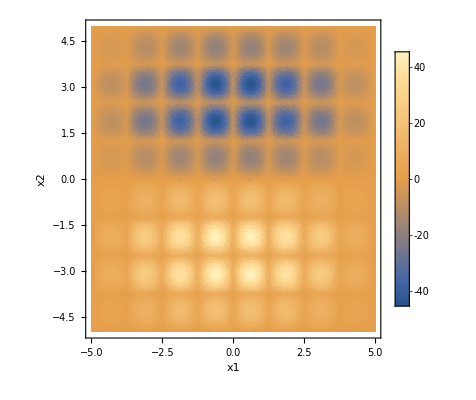

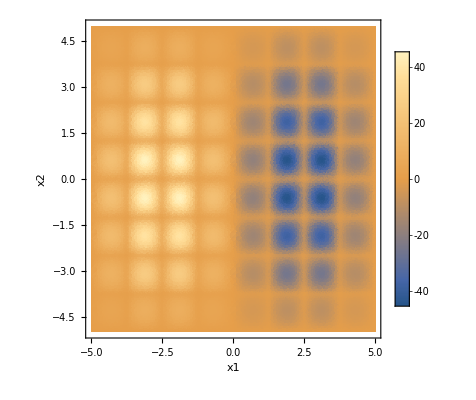

```mathematica
DensityPlot[Re[(DPFP1)]/.HeavisideTheta[0]->1, {x1, -intRange, intRange}, {x2, -intRange, intRange}, FrameLabel->{"x1", "x2"}, PlotLegends->Automatic,PlotRange->Full, PlotPoints->50]
DensityPlot[Re[DPFP2/.HeavisideTheta[0] -> 1], {x1, -intRange, intRange}, {x2, -intRange, intRange}, FrameLabel->{"x1", "x2"}, PlotLegends->Automatic,PlotRange->Full, PlotPoints->50]
```

### 3 Particle WF

```mathematica
(*TripplePartWF = onePartWF[x1][[1]]*onePartWF[x2][[2]] + onePartWF[x2][[1]]*onePartWF[x1][[2]];*)
```

```mathematica
expr = Det[{{A, b, c}, {F, G, H}, {J, d, k}}]
expr = ToString[expr]
expr = StringReplace[ expr, "-" -> "+"]
expr = ToExpression[expr]
```

c d F-A d H-c G J+b H J-b F k+A G k

c d F - A d H - c G J + b H J - b F k + A G k

c d F + A d H + c G J + b H J + b F k + A G k

c d F+A d H+c G J+b H J+b F k+A G k

```mathematica
testMatrix = {{A, b, c}, {F, G, H}, {J, d, k}}
```

{{A,b,c},{F,G,H},{J,d,k}}

```mathematica
testMatrix[[1,1]]
```

A

```mathematica
myS = "this is string "
StringReplace[myS, "string" -> "elephant"]
```

this is string

this is elephant

```mathematica
DensityPlot3D[2 Abs[(TriplePartWF)]^2/.HeavisideTheta[0]->1, {x1, -intRange, intRange}, {x2, -intRange, intRange},{x3, -intRange, intRange }, FrameLabel->{"x1", "x2","x3"}, PlotLegends->Automatic,PlotRange->Full, PlotPoints->50]
```

DensityPlot3D::optx: Unknown option FrameLabel→{x1,x2,x3} in DensityPlot3D[2 Abs[TriplePartWF]^2/.HeavisideTheta[0]→1,{x1,-intRange,intRange},{x2,-intRange,intRange},{x3,-intRange,intRange},FrameLabel→{x1,x2,x3},PlotLegends→Automatic,PlotRange→Full,PlotPoints→50].

DensityPlot3D[2 Abs[TriplePartWF]^2/.HeavisideTheta[0]→1,{x1,-intRange,intRange},{x2,-intRange,intRange},{x3,-intRange,intRange},FrameLabel→{x1,x2,x3},PlotLegends→Automatic,PlotRange→Full,PlotPoints→50]

### Probability calculations

```mathematica
gridlns
```

{-15/4,-5/2,-5/4,0,5/4,5/2,15/4,-5,5}

```mathematica
barrierPairs = {{-5, -5/3}, {-5/3, 5/3}, {5/3, 5}}
ntoprob = Range[1, Length[barrierPairs]]
```

{{-5,-5/3},{-5/3,5/3},{5/3,5}}

{1,2,3}

```mathematica
(*2p WF*)
```

```mathematica
(*TGDensity*)
nprob = (numBar+1)^2;
ngap = numBar +1;
```

```mathematica
pij[i_, j_]:= NIntegrate[Abs[DoublePartWF]^2, Flatten[{x1,barrierPairs[[i]]}], Flatten[{x2,barrierPairs[[j]]}],  WorkingPrecision-> 10]/DPWFNorm
```

```mathematica
probSingle= NIntegrate[Abs[DoublePartWF]^2, Flatten[{x1,barrierPairs[[1]]}], Flatten[{x2,barrierPairs[[1]]}]]/DPWFNorm
```

0.00382714

# Trying...keep trying

```mathematica
(*Fourier Transform*)
thisGraph = FourierTransform[Exp[-t^2] Sin[t],t,ω]
```

(ⅈ (-1+Cosh[ω]+Sinh[ω]) (Cosh[1/4 (1+ω)^2]-Sinh[1/4 (1+ω)^2]))/(2 √2)

```mathematica
thisGraph
Im[thisGraph]
```

(ⅈ (-1+Cosh[ω]+Sinh[ω]) (Cosh[1/4 (1+ω)^2]-Sinh[1/4 (1+ω)^2]))/(2 √2)

Re[(-1+Cosh[ω]+Sinh[ω]) (Cosh[1/4 (1+ω)^2]-Sinh[1/4 (1+ω)^2])]/(2 √2)

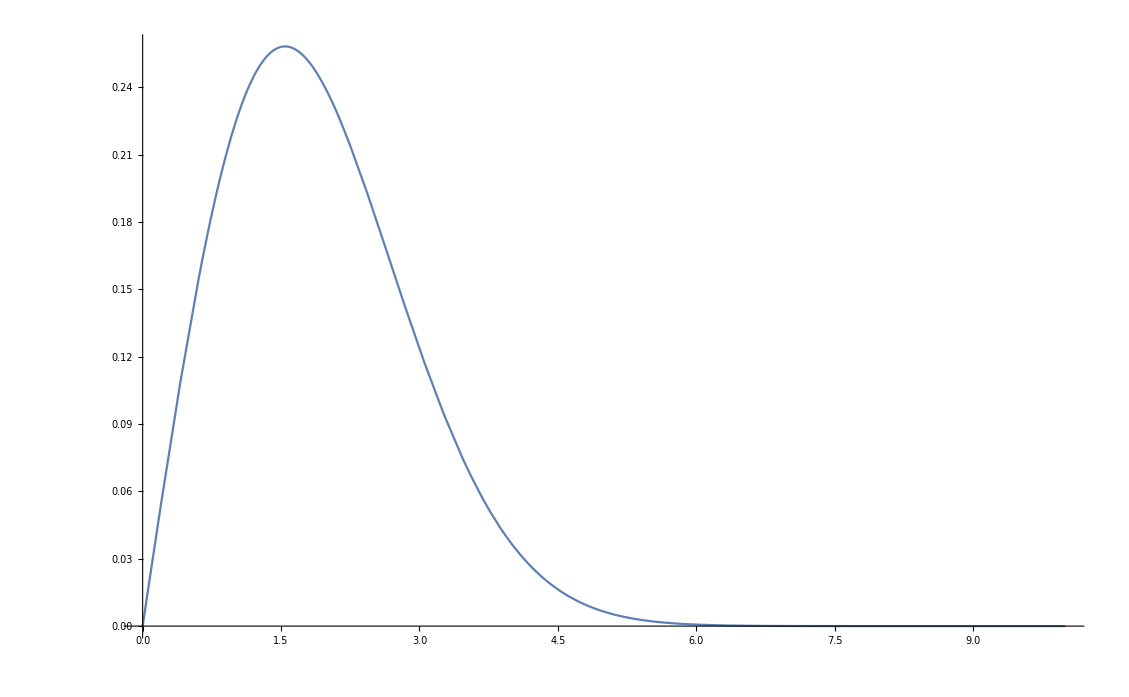

```mathematica
Plot[Im[thisGraph], {ω, 0, 10}, PlotRange->Automatic]
```